## Setup

This setup uses (n, η) = (u + v, D_u/D_vu+v) as variables.

### PDE solver

```mathematica
ClearAll@runTwoComponentSim;
Options[runTwoComponentSim]=Join[Options[NDSolve],{"GridPoints"->100,"BC"->"Reflective"}];
runTwoComponentSim[{f_,g_},params_,{nInit_,etaInit_},tMax_,opts:OptionsPattern[]]:=First@NDSolve[{
D[n[x,t],t]==Dv D[eta[x,t],{x,2}]+((f+g)/.{n->n[x,t],η->eta[x,t]}),D[eta[x,t],t]==Dv (1+d) D[eta[x,t],{x,2}]-Du D[n[x,t],{x,2}]+((g+d f)/.{n->n[x,t],η->eta[x,t]}),
If[OptionValue["BC"]==="Periodic",
{(* periodic BCs *)
n[0,t]==n[L,t],eta[0,t]==eta[L,t],(D[n[x,t],x]/.x->0)==(D[n[x,t],x]/.x->L),(D[eta[x,t],x]/.x->0)==(D[eta[x,t],x]/.x->L)
},
{(* no-flux BCs *)
(D[n[x,t],x]/.x->0)==0,(D[eta[x,t],x]/.x->0)==0,(D[n[x,t],x]/.x->L)==0,(D[eta[x,t],x]/.x->L)==0
}
],
(* initial condition *)
n[x,0]==nInit[x],
eta[x,0]==etaInit[x]
}/.params,
{n,eta},
{x,0,L/.params},
{t,0,tMax},
Evaluate[Sequence@@FilterRules[List@opts,Options[NDSolve]]],Method->{"MethodOfLines","SpatialDiscretization"->{"TensorProductGrid","MinPoints"->OptionValue["GridPoints"],"MaxPoints"->OptionValue["GridPoints"],AccuracyGoal->0,PrecisionGoal->0,"DifferenceOrder"->2},(*Choose higher scale factor to enforce boundary conditions in case the initial condition does not fulfil them*)"DifferentiateBoundaryConditions"->{True,"ScaleFactor"->1},"Method"->{"IDA","ImplicitSolver"->"Newton"}}
];
```

### Finite difference equations for stationary state

```mathematica
discreteLaplace[data_,dx_]:=With[{paddedData=Join[{data[[1]]},data,{data[[-1]]}]},
Differences[paddedData,2]/dx^2
]
```

```mathematica
ClearAll@setupFiniteDifferenceEqs;
setupFiniteDifferenceEqs[f_,g_,gridRes_]:=With[{
nVec=Thread[n@Range[gridRes]],
etaVec=Thread[eta@Range[gridRes]]
},
<|
"UnitGrid"->Range[0.5/gridRes,1,1./gridRes],
"nVec"->nVec,
"etaVec"->etaVec,
"Vars"->Join[nVec,etaVec],
"Eqs"->{
Dv discreteLaplace[etaVec,L/gridRes]+((f+g)/.{n->nVec,η->etaVec}),
Dv (1+d) discreteLaplace[etaVec,L/gridRes]-Du discreteLaplace[nVec,L/gridRes]+((g+d f)/.{n->nVec,η->etaVec})
}
|>
]
```

```mathematica
getInitGuess[fdSetup_,params_,initSol_]:=Join[
Transpose[{
fdSetup["nVec"],
n[x,T]/.params/.initSol/.x->(L/.params) fdSetup["UnitGrid"]
}],
Transpose[{
fdSetup["etaVec"],
eta[x,T]/.params/.initSol/.x->(L/.params) fdSetup["UnitGrid"]
}]
]
```

### Model setup

Brusselator reation kinetics, transformed to (n,η) variables

```mathematica
f=u^2 v-u+eps(p-u)/.{u->(n-η)/(1-d),v->(η-d n)/(1-d)};
g=-u^2 v+u/.{u->(n-η)/(1-d),v->(η-d n)/(1-d)};
```

```mathematica
fixedParams=Join[{d->Du/Dv/.#},#]&@{
Du->1/10,Dv->1,p->2,
T->100000
};
```

```mathematica
fdSetup=setupFiniteDifferenceEqs[f,g,200];
```

### Setup test / usage example

```mathematica
testParams=Join[{L->20},fixedParams];
```

```mathematica
testRun=runTwoComponentSim[
{f,g},
Join[{eps->10^-4},testParams],
{
3 √(d/2)+(1-d)√(2/d)/2(1-Tanh[(#-L xi)/(2 √Du)])&,
3 √(d/2)&
}/.xi->p/√(2/d),
T/.testParams
];
```

```mathematica
testSol=Block[{n,eta},FindRoot[
fdSetup["Eqs"]/.Join[{eps->10^-4},testParams],
getInitGuess[fdSetup,testParams,testRun],
MaxIterations->100
]
];
```

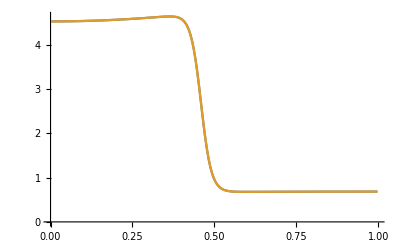

```mathematica
ListLinePlot[{
Transpose[{x,n[L x,T]/.testParams/.testRun}/.x->fdSetup["UnitGrid"]],
Transpose[{fdSetup["UnitGrid"],fdSetup["nVec"]/.testSol}]
}]
```

### Continuation setup and test / usage example

Load continuation code from separate setup file.

```mathematica
NotebookEvaluate[NotebookDirectory[]<>"continuation-setup.nb",
InsertResults->False
];
```

```mathematica
contData=arclengthContinuation[
Flatten@fdSetup["Eqs"], (* stat state equations *)
Join[{eps->10^-4},testParams], (* initial parameters *)
testSol, (* init solution *)
eps, (* continuation parameter *)
10^-4,(* init step size in the arclength parameter s *)
"ParamDomain"->{0,1},
"MaxSteps"->200,"MaxStepSize"->0.1,
"TangentAlignmentThreshold"->0.99,
"TerminateAtFold"->False
];//AbsoluteTiming
```

{30.3579,Null}

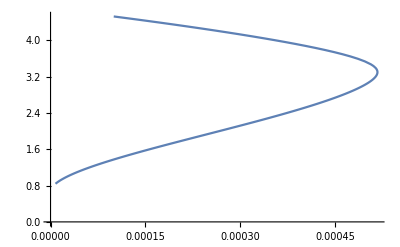

```mathematica
ListLinePlot[contData["CurveData"][[All,1,{-1,1}]]]
```

### Quadratic interpolation to find fold location

```mathematica
With[{
fit=First@Solve[{f[x1]==y1,f[x2]==y2,f[x3]==y3}/.f[x_]:>a x^2+b x+c,{a,b,c}]
},
fitParabola[p:{{_,_},{_,_},{_,_}}]:=fit/.{
x1->p[[1,1]],x2->p[[2,1]],x3->p[[3,1]],
y1->p[[1,2]],y2->p[[2,2]],y3->p[[3,2]]
}
];
With[{
parabolaMaximum={x,a x^2+b x+c}/.First@Solve[D[a x^2+b x+c,x]==0,x]
},
quadraticInterpolateMaximum[points:{{_,_},{_,_},{_,_}}]:=parabolaMaximum/.fitParabola@points
];
```

#### Example

30

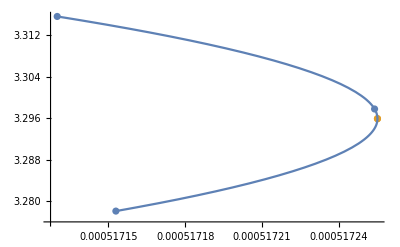

```mathematica
WithCascading[{
epsFold=Max[contData["CurveData"][[All,1,-1]]],
foldIndex=First @FirstPosition[contData["CurveData"][[All,1,-1]],epsFold],
points=contData["CurveData"][[foldIndex+{-1,0,1},1,{1,-1}]]
},
Print@foldIndex;
Show[
ListPlot[{
Reverse/@points,
Reverse/@{quadraticInterpolateMaximum@points}
}
],
ParametricPlot[{Evaluate[a x^2+b x+c/.fitParabola@points],x},{x,points[[1,1]],points[[-1,1]]}]
]
]
```

```mathematica
Position[Times@@#&/@Partition[Sign[contData["CurveData"][[All,1,-1]]-4.5 10^-4],2,1],-1]
```

{{19},{75}}

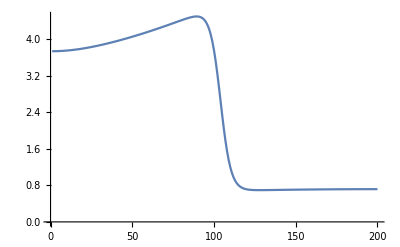

```mathematica
ListLinePlot[contData["CurveData"][[19,1,1;;Length@fdSetup["UnitGrid"]]]]
```

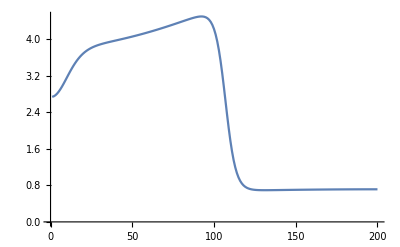

```mathematica
ListLinePlot[contData["CurveData"][[75,1,1;;Length@fdSetup["UnitGrid"]]]]
```

### Setup: function to locate fold by continuation in ϵ

```mathematica
findFold[params_,{epsInit_,epsMax_}]:=Block[{initRun,initSol,contData},
initRun=runTwoComponentSim[
{f,g},
Join[{eps->epsInit},params],
{
3 √(d/2)+(1-d)√(2/d)/2(1-Tanh[(#-L xi)/(2 √Du)])&,
3 √(d/2)&
}/.xi->p/√(2/d),
T/.params
];
initSol=Block[{n,eta},FindRoot[
fdSetup["Eqs"]/.Join[{eps->epsInit},params],
getInitGuess[fdSetup,params,initRun],
MaxIterations->500
]
];
contData=arclengthContinuation[
Flatten@fdSetup["Eqs"],
Join[{eps->epsInit},params],
initSol,
eps,10^-4,
"ParamDomain"->{0,epsMax},
"MaxSteps"->1000,"MaxStepSize"->0.1,
"TangentAlignmentThreshold"->0.99,
"TerminateAtFold"->True (* stop continuation after passing fold *)
];
If[
contData["TerminationReason"]=="Fold",
{
contData,
quadraticInterpolateMaximum@contData["CurveData"][[-3;;-1,1,{1,-1}]]
},
Print["No fold found. Try increasing MaxSteps."];
{
contData,
{0,0}
}
]
]
```

```mathematica
testData=findFold[Join[{L->20},fixedParams],{10^-5,1}];//AbsoluteTiming
```

{6.09924,Null}

```mathematica
testData[[2]]
```

quadraticInterpolateMaximum[{{3.315,0.000517137},{3.29874,0.000517252},{3.28096,0.000517183}}]

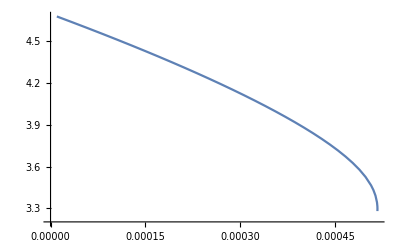

```mathematica
ListLinePlot[testData[[1]]["CurveData"][[All,1,{-1,1}]]]
```

## (L,ϵ) sweep

### Analytic approx (Eq. 55 in the supplement)

```mathematica
etaLat=2 √d;
etaInf=3 √(d/2);
up=√(2/d);
epsCrit=(2 Dv)/(p/up L)^2 Abs[etaLat-etaInf]/Abs[p-up]/.fixedParams;
```

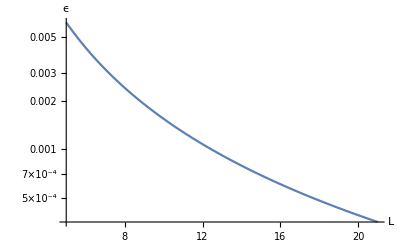

```mathematica
LogPlot[epsCrit,{L,5,21},AxesLabel->{L,ϵ}]
```

```mathematica
theoryTableSplitting=Table[{
epsCrit,L
},
{L,5,21,0.5}
];
```

### Run fold sweep

```mathematica
Off[FindRoot::lstol]
```

```mathematica
LSweepFold=Monitor[
Table[{
LIter,
findFold[Join[{L->LIter},fixedParams],{10^-5,1}]
},
{LIter,5,21,2}
],
LIter
];//AbsoluteTiming
```

{97.8127,Null}

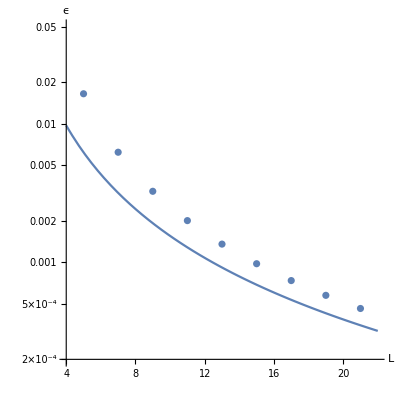

```mathematica
Show[
ListLogPlot[
{#[[1]],#[[2,2,2]]}&/@LSweepFold,
PlotRange->{{4,22},{2 10^-4,0.05}}
],
LogPlot[epsCrit,{L,4,22}],
AspectRatio->1,
AxesLabel->{L,ϵ}
]
```

```mathematica
Export[NotebookDirectory[]<>"mesa-splitting_eps-L-table.txt",{#[[1]],#[[2,2,2]]}&/@LSweepFold,"Table"]
```

/Users/Fridtjof.Brauns/Mathematica Projects/Coarsening Standalone/mesa-splitting_eps-L-table.txt

## Combined plot

Load data exported from interrupted-coarsening_Brusselator.nb

```mathematica
coarseningData=Import[NotebookDirectory[]<>"interrupted-coarsening_eps-L-table.txt","Table"];
```

```mathematica
theoryTableCoarsening=Table[
{
epsIter,
Λ/.FindRoot[
epsIter Λ/(12 √Du)==(1-ξ)^-2 Exp[-ξ Λ/√Du]/.ξ->p/√(2/d)/.fixedParams,
{Λ,0}
]
},
{epsIter,10^Range[-12,-1,0.5]}
];
```

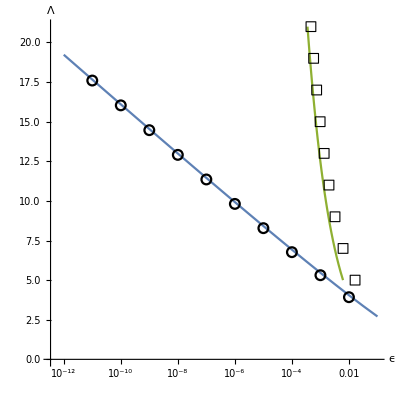

```mathematica
ListLogLinearPlot[{
theoryTableCoarsening,
coarseningData,
theoryTableSplitting,
{#[[2,2,2]],#[[1]]}&/@LSweepFold
},
Joined->{True,False,True,False},
AspectRatio->1,
PlotMarkers->{
None,{Graphics@{Black,Circle[]},Medium},
None,{Graphics@{FaceForm[None],EdgeForm[{Black}],Rectangle[]},Medium}
},
BaseStyle->14,
AxesLabel->{ϵ,Λ}
]
```